```mathematica
SetDirectory@NotebookDirectory[]
Import["esmlib_nsl.wl"]
```

/home/eric/git/nonlinear-systems-lab

## Forward Euler

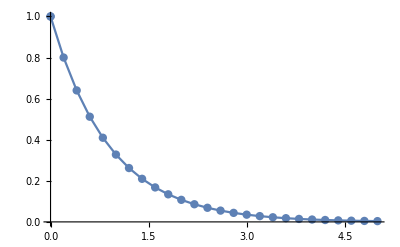

```mathematica
myNDsolve[eqn_,initial_,func_,{ivar_,start_,end_,deltat_}]:=Module[{xs,ys,update,deriv},
xs={start};
ys={func[start]/.Solve[initial,func[start]][[1]]};

deriv=Solve[eqn,func'[ivar]][[1,1,2]];

update[t_]:=Module[{dt,m},
dt=t-xs[[-1]];
m=deriv/.{func[ivar]->ys[[-1]],ivar->xs[[-1]]};
AppendTo[xs,t];
AppendTo[ys,ys[[-1]]+m*dt];
(*Print[t];*)
];
Do[update[t],{t,start,end,deltat}];

{xs,ys}
]

eqn = y'[t]==-y[t];
initialCond=y[0]==1;

{xs,ys}=myNDsolve[eqn,initialCond,y,{t,0,5,.2}];

ListLinePlot[Transpose@{xs,ys},Mesh->All,PlotRange->{All,All}]
```

## NDSolve with Matrices

```mathematica
x0={1,0};
a=({{0, 1}, {-1, 0}});
```

{x→InterpolatingFunction[{{0., 10.}}, <>]}

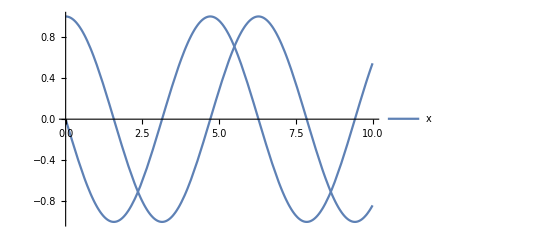

```mathematica
sol=NDSolve[{x'[t]==a.x[t],x[0]==x0},x,{t,0,10}][[1]]
IFPlot[sol]
```